## Integral

Let 𝒮 be the set of all differentiable functions with continuous derivatives f:[0,1]->ℝ such that

```mathematica
ℰ[f_]:=∫_0^1 f(x)ⅆx==∫_0^1 x f(x)ⅆx==1
```

The goal is to compute the infimum for f∈𝒮 of

```mathematica
ℐ[f_]:=∫_0^1 (f'(x))^2 ⅆx
```

Observe that since ∫_0^1 1ⅆx==1 then

∫_0^1 (f(x)-1)ⅆx==∫_0^1 (x f(x)-1)ⅆx==0

Define a suitable Lagrangian with arbitrary parameters α and β:

```mathematica
ℒ[f_]:=x↦(f'(x))^2+α (f(x)-1)+β (x f(x)-1)
```

Apply the Euler-Lagrange equation:

```mathematica
(∂ℒ[f][x])/(∂f(x))==Subscript[ⅆ, x](∂ℒ[f][x])/(∂f'(x))
```

α+β x==2 f''(x)

Solve this ODE:

```mathematica
f=DSolveValue[%,f,x]
```

{x}↦1/4 ((β x^3)/3+α x^2)+2 x+1

Determine 1 and 2 by requiring that ℰ[f] holds:

```mathematica
ℰ[f]
```

α/12+β/48+1+2/2==α/16+β/60+1/2+2/3==1

```mathematica
coefs=First@Solve[%,{1,2}]
```

{1→1/120 (5 α+2 β-240),2→1/40 (-10 α-3 β+240)}

Express the general solution to the problem:

```mathematica
f=f/.coefs
```

{x}↦1/120 (5 α+2 β-240)+1/4 ((β x^3)/3+α x^2)+1/40 x (-10 α-3 β+240)

Compute ℐ[f]:

```mathematica
ℐ[f]
```

α^2/48+(α β)/48+(9 β^2)/1600+β/10+36

Compute the infimum by determining the values of α and β that minimize ℐ[f]:

```mathematica
Minimize[α^2/48+(α β)/48+(9 β^2)/1600+β/10+36,{α,β}]
```

{30,{α→60,β→-120}}

So the infimum is 30.

In addition we have determined the function for which the infimum is achieved:

```mathematica
f=f/.Last[%];
```

```mathematica
Simplify@f(x)
```

-10 x^3+15 x^2-3/2

```mathematica
f'(x)//Factor
```

-30 (x-1) x

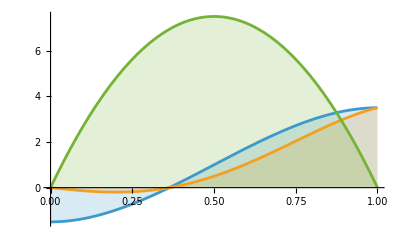

```mathematica
Plot[{f(x),x f(x),f'(x)},{x,0,1},Filling->Axis]
```

### Yuepeng Alex Yang

It's a very sneaky manipulation: my biggest advice for you is to experiment and mess around with the integrals f(x) and xf(x) by using integration by parts.

If you do it correctly, you should notice that 
\int_0^1 xf'(x)dx + f(1) =1 and \int_0^1 (x^2/2)f'(x)dx + f(1)/2 = 1.  
These two equations gives you \int_0^1 (x^2-x)f'(x)dx = 1.

```mathematica
∫_0^1 x f'(x)ⅆx==(x f(x)/.x->1)-(x f(x)/.x->0)-∫_0^1 f(x)ⅆx==f(1)-1
```

∫_0^1 x f'(x)ⅆx==f(1)-∫_0^1 f(x)ⅆx==f(1)-1

```mathematica
∫_0^1 x^2 f'(x)ⅆx==(x^2 f(x)/.x->1)-(x^2 f(x)/.x->0)-2∫_0^1 x f(x)ⅆx==f(1)-2
```

∫_0^1 x^2 f'(x)ⅆx==f(1)-2 ∫_0^1 x f(x)ⅆx==f(1)-2

```mathematica
∫_0^1 (x^2-x) f'(x)ⅆx== (f(1)-2)-(f(1)-1)//Simplify
```

∫_0^1 (x-1) x f'(x)ⅆx==-1

By Cauchy-Schwarz Inequality:

```mathematica
1≤(∫_0^1 (x^2-x) f'(x)ⅆx)^2≤(∫_0^1 (x^2-x)^2 ⅆx) (∫_0^1 (f'(x))^2 ⅆx)
```

We know that \int_0^1 (x^2-x)^2 dx = 1/30.

```mathematica
∫_0^1 (x^2-x)^2 ⅆx
```

1/30

Thus, 30<= \int (f'(x))^2dx. So our infimum is 30.

```mathematica
30≤∫_0^1 (f'(x))^2 ⅆx
```

### Direct Solution

Assume a cubic polynomial:

```mathematica
sol=First@Solve@ℰ[x↦α+β x+γ x^2+δ x^3]
```

{γ→-18 α-4 β-12,δ→20 α+(10 β)/3+20}

```mathematica
ℐ[x↦α+β x+γ x^2+δ x^3/.sol]//Expand
```

72 α^2+16 α β+216 α+β^2+24 β+192

```mathematica
Minimize[%,{α,β}]
```

{30,{α→-3/2,β→0}}

```mathematica
α+β x+γ x^2+δ x^3/.sol/.Last[%]
```

-10 x^3+15 x^2-3/2

### Jean-Pierre Barani

```mathematica
⟨f_,g_⟩:=∫_0^1 f(x)g(x)ⅆx
```

```mathematica
⟨f,x↦1⟩==1
```

∫_0^1 f(x)ⅆx==1

```mathematica
⟨f,x↦x⟩==1
```

∫_0^1 x f(x)ⅆx==1

```mathematica
ℱ[x_]:=f(x)==a+∫_0^x g(y)ⅆy
```

```mathematica
ℱ[0]
```

f(0)==a

```mathematica
(∂ℱ(x))/(∂x)
```

f'(x)==g(x)

Define ℯ_i:

```mathematica
Subscript[ℯ, i_](y_):=1-y^i
```

Compute ⟨g,ℯ_i⟩==⟨f',ℯ_i⟩ for i=1, 2:

```mathematica
⟨f',Subscript[ℯ, 1]⟩==((1-x)f(x)/.x->1)-((1-x)f(x)/.x->0)+∫_0^1 f(x)ⅆx==1-a
```

∫_0^1 (1-x) f'(x)ⅆx==∫_0^1 f(x)ⅆx-f(0)==1-a

```mathematica
⟨f',Subscript[ℯ, 2]⟩==((1-x^2)f(x)/.x->1)-((1-x^2)f(x)/.x->0)+2∫_0^1 x f(x)ⅆx==2-a
```

∫_0^1 (1-x^2) f'(x)ⅆx==2 ∫_0^1 x f(x)ⅆx-f(0)==2-a

Write h==α ℯ_1+β ℯ_2:

```mathematica
h=x↦α Subscript[ℯ, 1](x)+β Subscript[ℯ, 2](x);
```

```mathematica
⟨h,Subscript[ℯ, 1]⟩==1-a
```

α/3+(5 β)/12==1-a

```mathematica
⟨h,Subscript[ℯ, 2]⟩==2-a
```

(5 α)/12+(8 β)/15==2-a

```mathematica
Solve[{%%,%},{α,β}]//First
```

{α→-4 (7 a+18),β→20 (a+3)}

Compute Norm[h]==⟨h,h⟩:

```mathematica
⟨h,h⟩/.%//Factor
```

8 (a^2+3 a+6)

Complete the square:

```mathematica
8((a+3/2)^2+(6-9/4))
```

8 ((a+3/2)^2+15/4)

```mathematica
%/.a->-3/2
```

30

```mathematica
{α->-4 (7 a+18),β->20 (a+3)}/.a->-3/2
```

{α→-30,β→30}

```mathematica
h(x)/.%
```

30 (1-x^2)-30 (1-x)

```mathematica
Factor@%
```

-30 (x-1) x

#### Alternative Basis

```mathematica
Subscript[𝕖, i_](y_):=y^i
```

Compute ⟨g,𝕖_i⟩==⟨f',𝕖_i⟩ for i=1, 2:

```mathematica
⟨f',Subscript[𝕖, 1]⟩==(x f(x)/.x->1)-(x f(x)/.x->0)-∫_0^1 f(x)ⅆx==f(1)-1
```

∫_0^1 x f'(x)ⅆx==f(1)-∫_0^1 f(x)ⅆx==f(1)-1

```mathematica
⟨f',Subscript[𝕖, 2]⟩==(x^2 f(x)/.x->1)-(x^2 f(x)/.x->0)-2∫_0^1 x f(x)ⅆx==f(1)-2
```

∫_0^1 x^2 f'(x)ⅆx==f(1)-2 ∫_0^1 x f(x)ⅆx==f(1)-2

Write h==α 𝕖_1+β 𝕖_2:

```mathematica
h=x↦α Subscript[𝕖, 1](x)+β Subscript[𝕖, 2](x);
```

```mathematica
⟨h,Subscript[𝕖, 1]⟩==f(1)-1
```

α/3+β/4==f(1)-1

```mathematica
⟨h,Subscript[𝕖, 2]⟩==f(1)-2
```

α/4+β/5==f(1)-2

```mathematica
Solve[{%%,%},{α,β}]//First
```

{α→-12 (f(1)-6),β→20 (f(1)-5)}

Compute Norm[h]==⟨h,h⟩:

```mathematica
⟨h,h⟩/.%//Factor
```

8 ((f(1))^2-7 f(1)+16)

Complete the square:

```mathematica
8((f(1)-7/2)^2+(16-49/4))
```

8 ((f(1)-7/2)^2+15/4)

```mathematica
%/.f(1)->7/2
```

30

```mathematica
{α->-12 (f(1)-6),β->20 (f(1)-5)}/.f(1)->7/2
```

{α→30,β→-30}

```mathematica
h(x)/.%
```

30 x-30 x^2